## Amp power supply modelling

i : input voltage
o : output voltage
c : capicator charge
m : capicator maximum charge capacity
p : power supply voltage
s: 1/(sampleRate*sagControl)
sagControl: a unitless quantity that allows us to adjust the speed of the sag effect while keeping m normalised at a value of 1.

```mathematica
Solve[o == (c + s( p (m-c) - o)) * i,o]//FullSimplify
```

{{o→(i (c-c p s+m p s))/(1+i s)}}

From above we see that output voltage can be represented as a product of two quantities:

o = i/(1+i s)  (c + p s(m-c))

The first part of this formula depends only on the input voltage and the sample rate. We call it the Asymptotic Limit function. In the definition below we apply the absolute value function to the input variable in the denominator to allow the function to work correctly for both positive and negative inputs. If the input signal is rectified before going through the gainstage then this is not necessary:

```mathematica
asymptoticLimitS[i_,s_]:=i/(1+Abs[i s])
```

When used independently of the power supply model, we can think of the asymptotic limit as simply a waveshaping function. It’s plot is shown below.

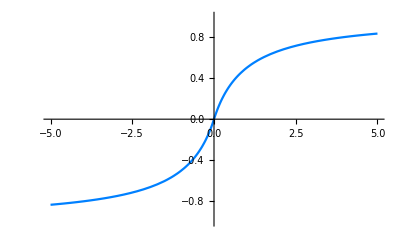

```mathematica
Plot[asymptoticLimitS[i,1],{i,-5,5},PlotStyle->Hue[7/12],ImageSize->Scaled[0.7],PlotRange->{-1,1}]
```

The second half of the formula for output voltage tells us that the output voltage is proportional to the charge in the capacitor and that the actual charge rate of the capacitor is proportional to (p - c), which is the portion of the charge capacity that remains uncharged. In other words, the charge rate decreases to zero as the capacitor approaches full charge (as c approaches p).

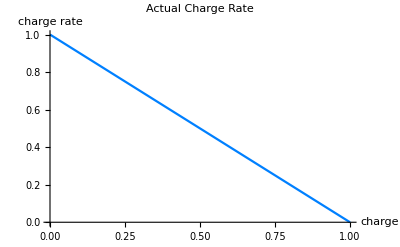

```mathematica
r=1;
p=1;
s = 1;
Plot[s r(p-c),{c,0,p},PlotStyle->Hue[7/12],PlotLabel->"Actual Charge Rate",AxesLabel->{"charge","charge rate"},ImageSize->Scaled[0.7]]
Clear[r,p]
```

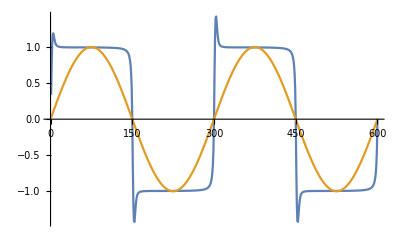

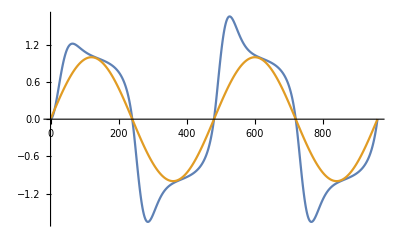

```mathematica
asymptoticLimitS[i_,s_]:=i/(1+Abs[s i])
c=0;
p=1;
r=0.05;
o=0;
s=1;
ig = 10;
outputVoltage[input_]:=Module[{},
c = c + r(p-c)- Abs[o];
o =asymptoticLimitS[input,s] (c +s r(p-c));
o/r
]

inputData =Sin[2π #/(300)]& /@ Range[600];
outputData = outputVoltage /@ (ig*inputData);
ListLinePlot[{outputData,inputData}]



c=0;
p=1;
r=0.05;
o=0;
scaleSampleRate = 48000;
sag = 1/400;
s= 1/(scaleSampleRate * sag);
outputVoltage[input_]:=Module[{},
c = c +s r(p-c)- s Abs[o];
o =asymptoticLimitS[input,s] (c +s r(p-c));
o/r
]

inputData = Sin[200π #/(scaleSampleRate)]& /@ Range[scaleSampleRate/50];
outputData = outputVoltage /@ (ig*inputData);
ListLinePlot[{outputData,inputData}]

Clear[c,p,r,o,s,ig];
```

```mathematica
Manipulate[
Plot[{2^s*asymptoticLimitS[i,2^s],asymptoticLimitS[i 2^s,1]},{i,-100,100},PlotStyle->{Hue[7/12],Directive[Hue[1/12],Dashed]},ImageSize->Scaled[0.7],PlotRange->{-1,1}],
{{s,0},-4,4}]
```

```mathematica
asymptoticLimitS[i_,s_]:=i/(1+Abs[s i])
asymptoticLimit[i_]:=i/(1+Abs[i])

Manipulate[
Module[{c,p,r,o,s,inputData,outputData1, outputData2,igv},
c=0;
p=1;
r=0.005;
o=0;
scaleSampleRate = 48000;
sag = 1/400;
s= 1/(scaleSampleRate * sag);

outputVoltage[input_]:=Block[{},
c = c +s r(p-c)- s Abs[o];
o =2^t asymptoticLimitS[input,s 2^t] (c +s r(p-c));
o/r
];

igv = 10^(ig/20);
 
inputData = Sin[200π #/(scaleSampleRate)]& /@ Range[scaleSampleRate/50];
outputData1 = outputVoltage /@ (igv*inputData);

scaleSampleRate = 12000;
sag = 1/400;
s= 1/(scaleSampleRate * sag);
c=0; o=0;
inputData = Sin[200π #/(scaleSampleRate)]& /@ Range[scaleSampleRate/50];
outputData2 = outputVoltage /@ (igv*inputData);
Show[ListLinePlot[{outputData1},DataRange->{0,1},PlotStyle->Hue[1/12]],ListLinePlot[{outputData2},DataRange->{0,1},PlotStyle->Hue[7/12]]]
],{ig,0,70},{{t,0},-4,4}]
```